```mathematica
Subdivide[0,1,2]
```

{0,1/2,1}

```mathematica
a=1
```

1

```mathematica
h=0.1
X={{0,0},{1/2,0},{0,.3}};
cent=Mean[X]
F[x_,y_]:=Dot[{x,y,1-x-y},X]
```

0.1

{1/6,0.1}

```mathematica
scale0=Norm@D[F[x,y],x]
scale1=Norm@D[F[x,y],y]
Norm[Cross[D[F[x,y],x],D[F[x,y],y]]]
```

0.3

0.583095

Cross::nonn1: 引数はすべて同じ長さのベクトルでなければなりません．また引数の個数はそれぞれの引数の要素数よりも1少なくなければなりません．

Norm[{0,-0.3}×{1/2,-0.3}]

```mathematica
Subdivide[0,1,Round[10/scale0]]
```

{0,1/33,2/33,1/11,4/33,5/33,2/11,7/33,8/33,3/11,10/33,1/3,4/11,13/33,14/33,5/11,16/33,17/33,6/11,19/33,20/33,7/11,2/3,23/33,8/11,25/33,26/33,9/11,28/33,29/33,10/11,31/33,32/33,1}

```mathematica
If[Round[5*Norm[F[x,1-x]-F[x,0]]]==0,{0},Subdivide[0,1-x,Round[1*Norm[F[x,1-x]-F[x,0]]]]]
```

If[Round[5 √(Abs[0.-0.3 (1-x)]^2+1/4 Abs[1-x]^2)]==0,{0},Subdivide[0,1-x,Round[1 Norm[F[x,1-x]-F[x,0]]]]]

```mathematica
(*sy[dh_(*y方向刻み*),x_]:=Module[{dH,n,L,ret},
L=Norm[F[x,0]-F[x,1-x]];
n=Round[L/dh];
dH=(1-x)/(n-1);
Table[dH*(i),{i,0,n-1,1}]
]
sx[dh_(*y方向刻み*)]:=Module[{dH,n,height,v,u,ret},
v=F[1,0]-F[0,0];
u=F[0,1]-F[0,0];
height=Norm[u-Dot[v,u]*Normalize[v]];
n=Round[height/dh];
dH=1/(n-1);
Table[dH*(i),{i,0,n-1,1}]
]*)
```

```mathematica
syOffset[dh_(*y方向刻み*),x_]:=Module[{dH,n,L,ret},
L=Norm[F[x,0]-F[x,1-x]];
n=Round[L/dh];
dH=(1-x)/(n);
ret=Table[dH*(i+1/2),{i,0,n-1,1}];
If[Length[ret]==0,{0},ret]
]
sxOffset[dh_(*y方向刻み*)]:=Module[{dH,n,height,v,u,ret},
v=F[0,1]-F[0,0];
u=F[1,0]-F[0,0];
height=Norm[u-Dot[v,Normalize[u]]*Normalize[v]];
n=Round[height/dh];
dH=1/(n);
ret=Table[dH*(i+1/2),{i,0,n-1,1}];
If[Length[ret]==0,{0},ret]
]
```

```mathematica
Table[{x,sx[0.07,x]},{x,0.7,0.99,0.07}]
Table[{x,sy[0.07,x]},{x,0.7,0.99,0.07}]
```

{{0.7,sx[0.07,0.7]},{0.77,sx[0.07,0.77]},{0.84,sx[0.07,0.84]},{0.91,sx[0.07,0.91]},{0.98,sx[0.07,0.98]}}

{{0.7,sy[0.07,0.7]},{0.77,sy[0.07,0.77]},{0.84,sy[0.07,0.84]},{0.91,sy[0.07,0.91]},{0.98,sy[0.07,0.98]}}

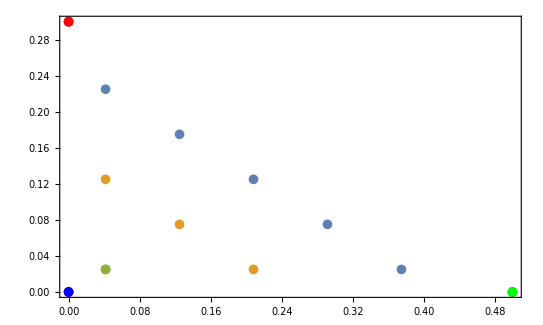

```mathematica
Show[
{ListPlot[{F[0,0],F[0,1],F[1,0]},AspectRatio->{{1,1},{1,1}},PlotStyle->{Red},Frame->True],
ListPlot[{F[0,0]},AspectRatio->{{1,1},{1,1}},PlotStyle->{Red},Frame->True],
ListPlot[{F[1,0]},AspectRatio->{{1,1},{1,1}},PlotStyle->{Blue},Frame->True],
ListPlot[{F[0,1]},AspectRatio->{{1,1},{1,1}},PlotStyle->{Green},Frame->True],
ListPlot[Table[F[x,y],{x,sxOffset[0.1]},{y,syOffset[0.1,x]}]]}
]
```